```mathematica
FITVALS :=Import["~/FIT_PARAM_READER/kmatrix_pole_plus_const_noCM.dat","Table"]
```

```mathematica
CORRS := Import["~/FIT_PARAM_READER/kmatrix_pole_plus_const_noCM.corrs.dat","Table"]
```

```mathematica
mPi:=0.0392
```

```mathematica
k[s_,m1_,m2_]:=Sqrt[(s-(m1+m2)^2)(s-(m1-m2)^2)/(4*s)]
```

```mathematica
K[s_,m_,g_,GAM0_]:=g^2/(m^2-s)+GAM0
```

```mathematica
T[s_,m_,g_,GAM0_]:=K[s,m,g,GAM0]/(1-Sqrt[-1]*(2k[s,mPi,mPi]/Sqrt[s])*K[s,m,g,GAM0])
```

```mathematica
For[i=1,i<Length[FITVALS[[1]]]+1,i++,FITVALNAMES=Append[FITVALNAMES,FITVALS[[i,1]]]]
```

```mathematica
FITVALNAMES
```

{JP0+_g_pi:pi/1^S_0_pole0,JP0+_gamma_pi:pi/1^S_0|pi:pi/1^S_0_order0,JP0+_m_pole0}

```mathematica
FITVALUES={}
```

{}

```mathematica
For[i=1,i<Length[FITVALS[[1]]]+1,i++,FITVALUES= Append[FITVALUES,FITVALS[[i,2]]]]
```

```mathematica
FITVALUES
```

{-0.122043,-0.665411,0.128297}

```mathematica
FITERRORS={}
```

{}

```mathematica
For[i=1,i<Length[FITVALS[[1]]]+1,i++,FITERRORS= Append[FITERRORS,FITVALS[[i,3]]]]
```

```mathematica
FITERRORS
```

{0.0245674,0.555705,0.00415995}

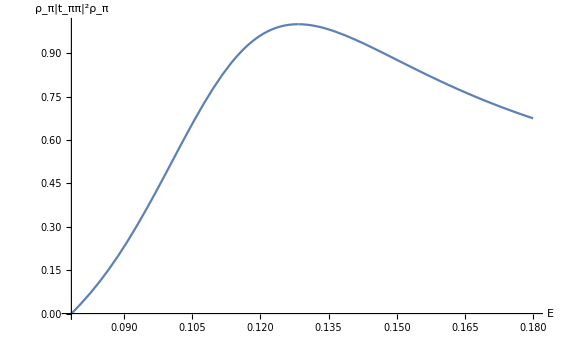

```mathematica
Plot[Abs[(2*k[E^2,mPi,mPi]/E)*T[E^2,FITVALUES[[3]],FITVALUES[[1]],FITVALUES[[2]]]]^2,{E,mPi*2,0.18},AxesLabel->{"E","ρ_π|t_ππ|^2ρ_π"}]
```